```mathematica
(* In this script, the neutrino transition probabilities are calculated and plotted. 
Notation wise, NH=Normal Hierarchy, IH=Inverted Hierarchy,EU=Early Universe and LU=Late Universe. We start by listing the parameters needed, which are retrieved from the ``Review of Particle Physics'', reference [32] of the manuscript.*)
Co[x_]:=Cos[x];
S[x_]:=Sin[x];
(*This is Subscript[θ, 12]*)
a=ArcSin[Sqrt[0.307]];
(*This is Subscript[θ, 13]*)
b=ArcSin[Sqrt[0.0218]];
(*This is Subscript[θ, 23] in the NH*)
NHc=ArcSin[Sqrt[0.545]];
(*This is Subscript[θ, 23] in the IH*)
IHc=ArcSin[Sqrt[0.547]];
(*CP violating phase δ*)
d=1.04*Pi;
(*Subscript[Δm, 21]^2=Subscript[m, 2]^2-Subscript[m, 1]^2*)
Dm21=7.53*10^-5.;
(*Subscript[Δm, 32]^2=Subscript[m, 3]^2-Subscript[m, 2]^2 in the IH*)
Dm32IH=-2.546*10^-3.;
(*Subscript[Δm, 32]^2=Subscript[m, 3]^2-Subscript[m, 2]^2 in the NH*)
Dm32NH=2.453*10^-3.;
(*Subscript[Δm, 31]^2=Subscript[m, 3]^2-Subscript[m, 1]^2 in the NH*)
Dm31NH=Dm32NH+Dm21;
(*Subscript[Δm, 31]^2=Subscript[m, 3]^2-Subscript[m, 1]^2 in the IH*)
Dm31IH=Dm32IH+Dm21;
(*This is a typical neutrino energy detected at neutrino observatories. As long as the value is high enough to be in the ultra-high energy regime, the excat value does not affect the results*)
E0=10^16.;
(*In natural units, Subscript[H, 0]=2.13 x10^-33 xh. We keep this infinitesimal prefactor seperate to better study the effect of choosing different h.*)
H0=2.13*10^-33.;
fac=1/(H0*E0);
(*Matter density parameter as measured by the Planck mission (reference [3] in the mansucript)Subscript[Ω, m0]*)
Om0=0.315;
(*Dark Energy(DE) density parameter as measured by the Planck mission (reference [3] in the mansucript)Subscript[Ω, Λ0]*)
Ol0=0.685;
(*Hubble parameter at EU, i.e. h^EU*)
EUh=0.675;
(*Hubble parameter at LU, i.e. h^LU*)
LUh=0.732;
(*This is the integrand in eq.(11) of the mansucript*)
Subscript[F, Λ][z_]:= (Om0*(1+z)^7.+Ol0*(1+z)^4.)^-.5;
int=Assuming[z>=0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]];
(*This is Δλ of the mnasucript, eq.(11), for EU*)
EUomAn=int/EUh;
(*This is Δλ of the mnasucript, eq.(11), for LU*)
LUomAn=int/LUh;
(*This is the PMNS matrix, eq.(6) of the mnasucript, for NH*)
NHU={{Co[a]*Co[b],S[a]*Co[b],S[b]*(Co[d]-I*S[d])},{-S[a]*Co[NHc]-S[b]*S[NHc]*Co[a]*(Co[d]+I*S[d]),Co[a]*Co[NHc]-S[a]*S[NHc]*S[b]*(Co[d]+I*S[d]),S[NHc]*Co[b]},{S[a]*S[NHc]-S[b]*Co[a]*Co[NHc]*(Co[d]+I*S[d]),-S[NHc]*Co[a]-S[a]*S[b]*Co[NHc]*(Co[d]+I*S[d]),Co[b]*Co[NHc]}};
(*This is the PMNS matrix, eq.(6) of the mnasucript, for NH*)
IHU={{Co[a]*Co[b],S[a]*Co[b],S[b]*(Co[d]-I*S[d])},{-S[a]*Co[IHc]-S[b]*S[IHc]*Co[a]*(Co[d]+I*S[d]),Co[a]*Co[IHc]-S[a]*S[IHc]*S[b]*(Co[d]+I*S[d]),S[IHc]*Co[b]},{S[a]*S[IHc]-S[b]*Co[a]*Co[IHc]*(Co[d]+I*S[d]),-S[IHc]*Co[a]-S[a]*S[b]*Co[IHc]*(Co[d]+I*S[d]),Co[b]*Co[IHc]}};
```

```mathematica
(*U^† for NH*)
NHUdag=ConjugateTranspose[NHU];
(*U^† for IH*)
IHUdag=ConjugateTranspose[IHU];
(*The fllowing two lines are to check the Unitarity condition of the PMNS matrix, to make sure there was no error in writing them, for both NH and IH*)
MatrixForm[FullSimplify[NHUdag . NHU]];
MatrixForm[FullSimplify[IHUdag . IHU]];
```

```mathematica
(*Initial conditions: {1,0,0} for Neutron Decay; {0,1,0} for Muon Damping; {1/Sqrt[5],2/Sqrt[5],0} for Pion Decay*)
Psi0={1/Sqrt[5],2/Sqrt[5],0};
```

```mathematica
(*Initial condition for transition amplitude in the mass basis, Φ of the manuscript, in the NH and IH, respectively. Basically eq.(8) of the manuscript*)
NHPhi0=NHUdag . Psi0;
IHPhi0=IHUdag . Psi0;
```

```mathematica
(*The evolving factors for the mass basis transition amplitudes, as written in eq.(10) of the mnasucript*)
T=DiagonalMatrix[{Co[m1^2*Intz/2]-I*S[m1^2*Intz/2],Co[m2^2*Intz/2]-I*S[m2^2*Intz/2],Co[m3^2*Intz/2]-I*S[m3^2*Intz/2]}];
(*The evolved transition amplitude, in the mass basis, with redshift, as given in eq.(10) of the mansucript, for NH and IH, respectively*)
NHPhi=FullSimplify[T.NHPhi0];
IHPhi=FullSimplify[T.IHPhi0];
```

```mathematica
(*The evolved transition amplitude, in the flavor basis, with redshift, as given in eq.(10) of the mansucript, for NH and IH, respectively*)
NHPsi=NHU . NHPhi;
IHPsi=IHU . IHPhi;
(*Analytical expression for transition probability to Subscript[ν, e] for NH and IH, respectively*)
Print["NHPee="]
NHPee=FullSimplify[TrigReduce[ComplexExpand[Re[NHPsi[[1]]]^2+Im[NHPsi[[1]]]^2]]]
Print["IHPee="]
IHPee=FullSimplify[TrigReduce[ComplexExpand[Re[IHPsi[[1]]]^2+Im[IHPsi[[1]]]^2]]]
(*Analytical expression for transition probability to Subscript[ν, μ] for NH and IH, respectively*)
Print["NHPemu="]
NHPemu=FullSimplify[TrigReduce[ComplexExpand[Re[NHPsi[[2]]]^2+Im[NHPsi[[2]]]^2]]]
Print["IHPemu="]
IHPemu=FullSimplify[TrigReduce[ComplexExpand[Re[IHPsi[[2]]]^2+Im[IHPsi[[2]]]^2]]]
(*Analytical expression for transition probability to Subscript[ν, τ] for NH and IH, respectively*)
Print["NHPetau="]
NHPetau=FullSimplify[TrigReduce[ComplexExpand[Re[NHPsi[[3]]]^2+Im[NHPsi[[3]]]^2]]]
Print["IHPetau="]
IHPetau=FullSimplify[TrigReduce[ComplexExpand[Re[IHPsi[[3]]]^2+Im[IHPsi[[3]]]^2]]]
```

NHPee=

0.209126+0.0827733 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.016393 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0755059 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.00665245 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.000838373 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.0099709 Sin[1/2 Intz (m2-m3) (m2+m3)]

IHPee=

0.20881+0.083307 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.016552 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.0755652 Cos[1/2 Intz (m2-m3) (m2+m3)]-0.00664999 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.000854574 Sin[1/2 Intz (m1-m3) (m1+m3)]-0.00997452 Sin[1/2 Intz (m2-m3) (m2+m3)]

NHPemu=

0.432931-0.0321945 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0278105 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.427074 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00428892 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.00320191 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00760737 Sin[1/2 Intz (m2-m3) (m2+m3)]

IHPemu=

0.432852-0.032231 Cos[1/2 Intz (m1-m2) (m1+m2)]-0.0280357 Cos[1/2 Intz (m1-m3) (m1+m3)]+0.427415 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00428448 Sin[1/2 Intz (m1-m2) (m1+m2)]+0.00322008 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00760901 Sin[1/2 Intz (m2-m3) (m2+m3)]

NHPetau=

0.357944-0.0505788 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0442035 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.351568 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.00236354 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.00236354 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.00236354 Sin[1/2 Intz (m2-m3) (m2+m3)]

IHPetau=

0.358338-0.0510761 Cos[1/2 Intz (m1-m2) (m1+m2)]+0.0445876 Cos[1/2 Intz (m1-m3) (m1+m3)]-0.35185 Cos[1/2 Intz (m2-m3) (m2+m3)]+0.0023655 Sin[1/2 Intz (m1-m2) (m1+m2)]-0.0023655 Sin[1/2 Intz (m1-m3) (m1+m3)]+0.0023655 Sin[1/2 Intz (m2-m3) (m2+m3)]

```mathematica
(*Now that we have the general analytical expressions, we start specifiying for the cases EU and LU for each neutrino flavor. That is, we substitute the argument of the trigonometric functions that appeared before with the appropriate Δm^2 xΔλ for the four cases NH-EU, NH-LU, IH-EU,IH-LU.
Due the large value of 1/(Subscript[H, 0] Subscript[E, 0]), plotting the probabilities' evolution with redshift will result in numerical instabilities. To avoid that, we fist find the maximum value reached by every argument of the trigonometric functions above, e.g. Subscript[Δm, 12]^2xΔλ/2. Then we divide this value by 2π, to know how many cycles these functions are doing. The decimanl part of this division therefore contains the information we seek. To get the decimal part of Subscript[Δm, 12]^2 xΔλ/2π, we use:N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*)
```

```mathematica
Max21EU=MaxValue[{Dm21*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh,0<z<10},z];
Max21LU=MaxValue[{Dm21*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh,0<z<10},z];
Max31NHEU=MaxValue[{Dm31NH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh,0<z<10},z];
Max31NHLU=MaxValue[{Dm31NH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh,0<z<10},z];
Max31IHEU=MaxValue[{Abs[Dm31IH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh],0<z<10},z];
Max31IHLU=MaxValue[{Abs[Dm31IH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh],0<z<10},z];
Max32NHEU=MaxValue[{Dm32NH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh,0<z<10},z];
Max32NHLU=MaxValue[{Dm32NH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh,0<z<10},z];
Max32IHEU=MaxValue[{Abs[Dm32IH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/EUh],0<z<10},z];
Max32IHLU=MaxValue[{Abs[Dm32IH*Assuming[z≥0,Integrate[Subscript[F, Λ][zz],{zz,0,z}]]*fac/LUh],0<z<10},z];
```

```mathematica
(*NHEU*)
```

```mathematica
newPeeNHEU[z_]=NHPee/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*EUomAn*fac/(Max31NHEU)*N[Drop@@RealDigits[Round[N[Max31NHEU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*EUomAn*fac/(Max32NHEU)*N[Drop@@RealDigits[Round[N[Max32NHEU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*2*Pi)};
newPemuNHEU[z_]=NHPemu/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*EUomAn*fac/(Max31NHEU)*N[Drop@@RealDigits[Round[N[Max31NHEU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*EUomAn*fac/(Max32NHEU)*N[Drop@@RealDigits[Round[N[Max32NHEU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*2*Pi)};
newPetauNHEU[z_]=NHPetau/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*EUomAn*fac/(Max31NHEU)*N[Drop@@RealDigits[Round[N[Max31NHEU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*EUomAn*fac/(Max32NHEU)*N[Drop@@RealDigits[Round[N[Max32NHEU/(2*Pi)],1*^-3]]*10^-3//FromDigits]*2*Pi)};
```

```mathematica
(*NHLU*)
```

```mathematica
newPeeNHLU[z_]=NHPee/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*LUomAn*fac/(Max31NHLU)*N[Drop@@RealDigits[Round[N[Max31NHLU/(2*Pi)],1*^-7]]*10^-5//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*LUomAn*fac/(Max32NHLU)*N[Drop@@RealDigits[Round[N[Max32NHLU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi)};
newPemuNHLU[z_]=NHPemu/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*LUomAn*fac/(Max31NHLU)*N[Drop@@RealDigits[Round[N[Max31NHLU/(2*Pi)],1*^-7]]*10^-5//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*LUomAn*fac/(Max32NHLU)*N[Drop@@RealDigits[Round[N[Max32NHLU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi)};
newPetauNHLU[z_]=NHPetau/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31NH*LUomAn*fac/(Max31NHLU)*N[Drop@@RealDigits[Round[N[Max31NHLU/(2*Pi)],1*^-7]]*10^-5//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32NH*LUomAn*fac/(Max32NHLU)*N[Drop@@RealDigits[Round[N[Max32NHLU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi)};
```

```mathematica
(*IHEU*)
```

```mathematica
newPeeIHEU[z_]=IHPee/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-1]]*10^-1//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*EUomAn*fac/(Max31IHEU)*N[Drop@@RealDigits[Round[N[Max31IHEU/(2*Pi)],1*^-1]]*10^-1//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*EUomAn*fac/(Max32IHEU)*N[Drop@@RealDigits[Round[N[Max32IHEU/(2*Pi)],1*^-1]]*10^-1//FromDigits]*2*Pi)};
newPemuIHEU[z_]=IHPemu/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-1]]*10^-1//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*EUomAn*fac/(Max31IHEU)*N[Drop@@RealDigits[Round[N[Max31IHEU/(2*Pi)],1*^-1]]*10^-1//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*EUomAn*fac/(Max32IHEU)*N[Drop@@RealDigits[Round[N[Max32IHEU/(2*Pi)],1*^-1]]*10^-1//FromDigits]*2*Pi)};
newPetauIHEU[z_]=IHPetau/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*EUomAn*fac/(Max21EU)*N[Drop@@RealDigits[Round[N[Max21EU/(2*Pi)],1*^-1]]*10^-1//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*EUomAn*fac/(Max31IHEU)*N[Drop@@RealDigits[Round[N[Max31IHEU/(2*Pi)],1*^-1]]*10^-1//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*EUomAn*fac/(Max32IHEU)*N[Drop@@RealDigits[Round[N[Max32IHEU/(2*Pi)],1*^-1]]*10^-1//FromDigits]*2*Pi)};
```

```mathematica
(*IHLU*)
```

```mathematica
newPeeIHLU[z_]=IHPee/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*LUomAn*fac/(Max31IHLU)*N[Drop@@RealDigits[Round[N[Max31IHLU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*LUomAn*fac/(Max32IHLU)*N[Drop@@RealDigits[Round[N[Max32IHLU/(2*Pi)],1*^-6]]*10^-6//FromDigits]*2*Pi)};
newPemuIHLU[z_]=IHPemu/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*LUomAn*fac/(Max31IHLU)*N[Drop@@RealDigits[Round[N[Max31IHLU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*LUomAn*fac/(Max32IHLU)*N[Drop@@RealDigits[Round[N[Max32IHLU/(2*Pi)],1*^-6]]*10^-6//FromDigits]*2*Pi)};
newPetauIHLU[z_]=IHPetau/.{(m1-m2)*(m1+m2)*Intz->(-Dm21*LUomAn*fac/(Max21LU)*N[Drop@@RealDigits[Round[N[Max21LU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi),(m1-m3)*(m1+m3)*Intz->(-Dm31IH*LUomAn*fac/(Max31IHLU)*N[Drop@@RealDigits[Round[N[Max31IHLU/(2*Pi)],1*^-7]]*10^-7//FromDigits]*2*Pi),(m2-m3)*(m2+m3)*Intz->(-Dm32IH*LUomAn*fac/(Max32IHLU)*N[Drop@@RealDigits[Round[N[Max32IHLU/(2*Pi)],1*^-6]]*10^-6//FromDigits]*2*Pi)};
```

```mathematica
(*PLOTS*)
```

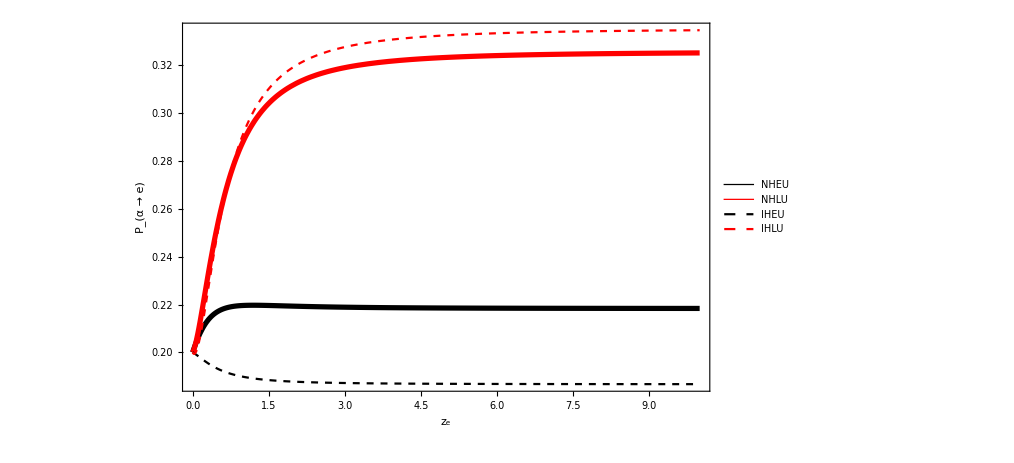

```mathematica
Plot[{newPeeNHEU[z],newPeeNHLU[z],newPeeIHEU[z],newPeeIHLU[z]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},PlotLegends->{"NHEU","NHLU","IHEU","IHLU"},FrameLabel->{"z_e","P_(α → e)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
```

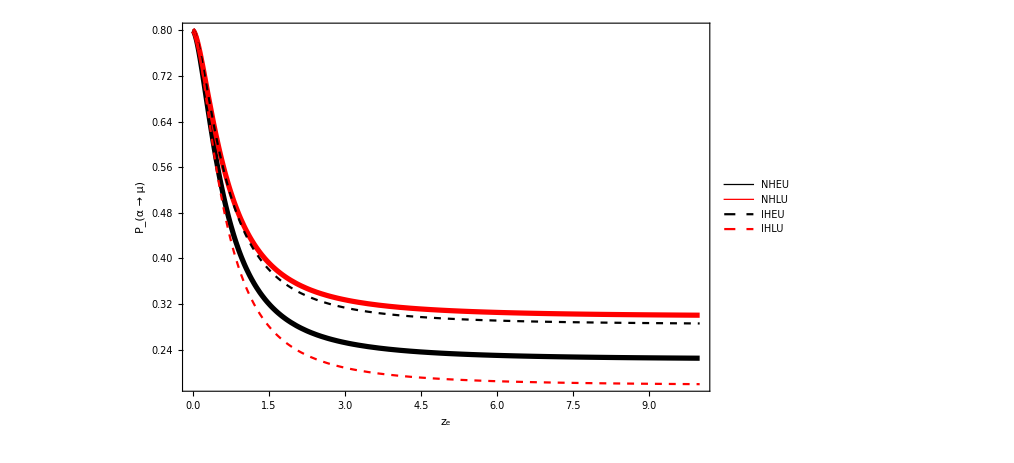

```mathematica
Plot[{newPemuNHEU[z],newPemuNHLU[z],newPemuIHEU[z],newPemuIHLU[z]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},PlotLegends->{"NHEU","NHLU","IHEU","IHLU"},FrameLabel->{"z_e","P_(α → μ)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
```

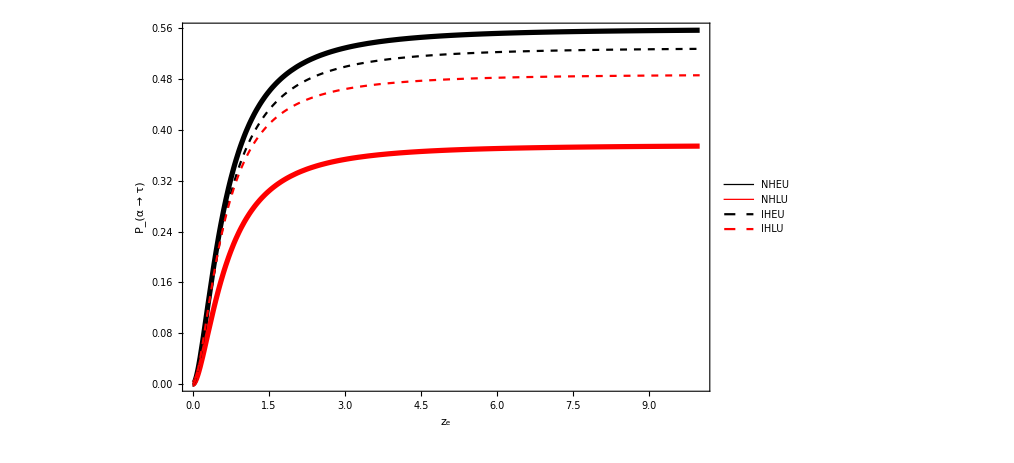

```mathematica
Plot[{newPetauNHEU[z],newPetauNHLU[z],newPetauIHEU[z],newPetauIHLU[z]},{z,0,10},ImageSize->750,Axes->False,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Directive[Thickness[0.005]]},{Black,Dashed},{Red,Dashed}},PlotLegends->{"NHEU","NHLU","IHEU","IHLU"},FrameLabel->{"z_e","P_(α → τ)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
```

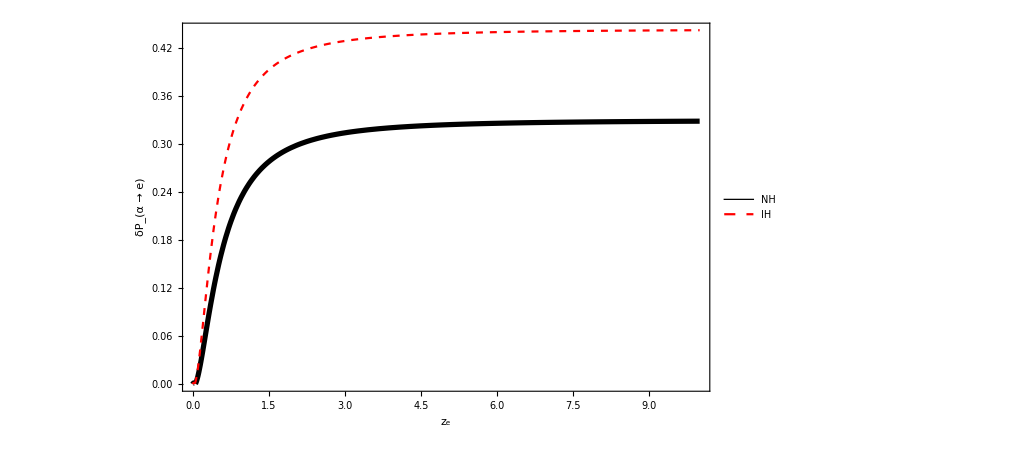

```mathematica
Plot[{Abs[(newPeeNHEU[z]-newPeeNHLU[z])/Max[newPeeNHLU[z],newPeeNHEU[z]]],Abs[(newPeeIHEU[z]-newPeeIHLU[z])/Max[newPeeIHLU[z],newPeeIHEU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},PlotLegends->{"NH","IH"},FrameLabel->{"z_e","δP_(α → e)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
```

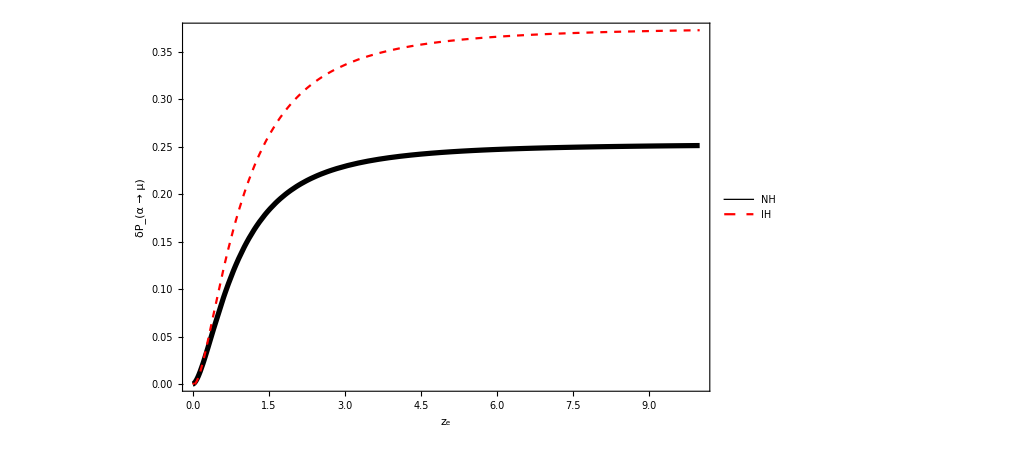

```mathematica
Plot[{Abs[(newPemuNHEU[z]-newPemuNHLU[z])/Max[newPemuNHLU[z],newPemuNHEU[z]]],Abs[(newPemuIHEU[z]-newPemuIHLU[z])/Max[newPemuIHLU[z],newPemuIHEU[z]]]},{z,0,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},PlotLegends->{"NH","IH"},FrameLabel->{"z_e","δP_(α → μ)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
```

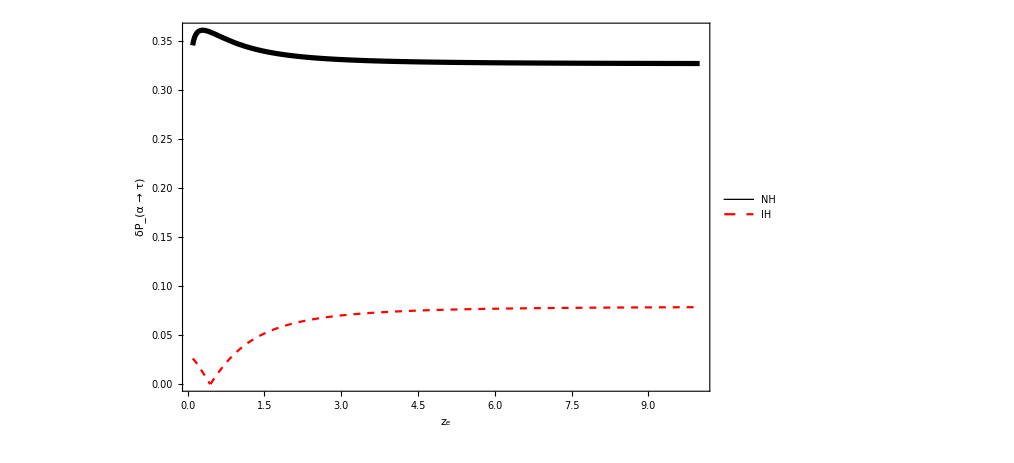

```mathematica
Plot[{Abs[(newPetauNHEU[z]-newPetauNHLU[z])/Max[newPetauNHLU[z],newPetauNHEU[z]]],Abs[(newPetauIHEU[z]-newPetauIHLU[z])/Max[newPetauIHLU[z],newPetauIHEU[z]]]},{z,0.1,10},ImageSize->750,Frame->True,PlotRange->All,PlotStyle-> {{Black,Directive[Thickness[0.005]]},{Red,Dashed}},PlotLegends->{"NH","IH"},FrameLabel->{"z_e","δP_(α → τ)"},RotateLabel->False,FrameStyle->Directive[Thickness[0.005],12,FontFamily->"Helvetica",Bold]]
```

```mathematica
(*VALUES FOR TERNARY PLOTS*)
```

```mathematica
Print["NHEU="];
Transpose[{newPemuNHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPetauNHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPeeNHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}]}]
Print["NHLU="];
Transpose[{newPemuNHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPetauNHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPeeNHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}]}]
Print["IHEU"];
Transpose[{newPemuIHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPetauIHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPeeIHEU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}]}]
Print["IHLU"];
Transpose[{newPemuIHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPetauIHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}],newPeeIHLU[{0.05,0.07,0.1,0.2,0.5,0.8,1,2,4}]}]
```

NHEU=

{{0.791221,0.00572428,0.203054},{0.784802,0.0110103,0.204187},{0.772874,0.021342,0.205784},{0.72101,0.0687745,0.210216},{0.556471,0.226379,0.21715},{0.443568,0.337202,0.21923},{0.39379,0.386585,0.219625},{0.284294,0.49638,0.219326},{0.239502,0.541825,0.218672}}

NHLU=

{{0.793041,0.00394193,0.203017},{0.787921,0.0073573,0.204722},{0.778378,0.0139587,0.207663},{0.736574,0.0440435,0.219382},{0.600516,0.145266,0.254218},{0.503351,0.218758,0.277892},{0.459202,0.252373,0.288425},{0.358207,0.329754,0.312039},{0.314813,0.363214,0.321973}}

IHEU

{{0.794942,0.00572633,0.199331},{0.790281,0.0106847,0.199034},{0.781168,0.0202626,0.19857},{0.739207,0.0638146,0.196978},{0.597885,0.209046,0.193069},{0.49625,0.313005,0.190745},{0.45017,0.360053,0.189776},{0.34536,0.466894,0.187747},{0.300713,0.51233,0.186956}}

IHLU

{{0.794422,0.00589379,0.199684},{0.788572,0.0109897,0.200438},{0.776894,0.0208123,0.202293},{0.722308,0.0651147,0.212577},{0.54087,0.208121,0.251009},{0.415734,0.305222,0.279044},{0.360971,0.347419,0.29161},{0.242237,0.438241,0.319522},{0.1947,0.474296,0.331004}}